```mathematica
ClearAll["Global`*"]; (* This function clears any past definitions of the variables *)



(* THERMOPHYSICAL PROPERTIES OF THE PARAFFIN *)

Tm=303; (* melting temprerature of the paraffin *)
ρs=880;ρl=760;ρ=ρl; (* density at solid and liquid states *)
ks=0.24;kl=0.15; (* thermal conductivity at solid and liquid states *)
cps=2.4*10^3;cpl=1.8*10^3; (* specific heat at solid and liquid states *)
q=179*10^3; (* latent heat of fusion*)
vd=3.42;vk=vd/ρ; (* dynamic viscosity (vd) and kinematic viscosity (vk) of paraffin *)


(* FORMULAS AND TRANSFORMATIONS*)

αs=ks/(ρs cps);αl=kl/(ρl cpl); (* thermal diffusivity at solid and liquid states *)
pr=vk/αl; (* Prandtl number*)
gdot=(G kl(T0-Tm))/R^2; (* heat sink parameter *)
ξ=gdot/(ρ q)((R^2 τ)/αl); (* mass proportion of liquid in the mixture; t taken as (r^2 τ)/αl *)
T0=Tm+(q ste)/cpl;(* temperature outside the sphere; it depends on the stefan number desired for the simulation *)

γ=ks/kl;
Γ=αs/αl;
θi=(Ti-Tm)/(T0-Tm); (* dimensionless initial temperature *)

λn=(n π)/splus;



keq=1;  (* equivalent thermal conductivity *)

(* since Rayleigh number = 0 (i.e. ≤ 5×10^4) for figure 3(c), keq is assumed equal to 1 *) 


(* PARAMETER VALUES *)

R=5*10^-2; (* radius of the sphere *)
Ti=295; (* initial temperature of the paraffin *)


(* PARAMETER VALUES SPECIFIC TO FIGURE 3(c) OF BECHIRI ET AL. 2020 *)

ste=0.05; (* Stefan number *)
ra=0; (* Rayleigh number *)
bi=10; (* Biot number *)
G=0; (* dimensionless heat sink parameter *)
```

```mathematica
θl=(-bi(√(keq τ)(Exp[-η^2/(4keq τ)]/η-Exp[-splus^2/(4keq τ)]/splus)+(√π)/2(Erfc[splus/(2 √(keq τ))]-Erfc[η/(2 √(keq τ))])))/(keq √(keq τ)Exp[-1/(4 keq τ)]-bi(√(keq τ)(Exp[-1/(4 keq τ)]-1/splus Exp[-splus^2/(4keq τ)])+(√π)/2(Erfc[splus/(2 √(keq τ))]-Erfc[1/(2 √(keq τ))])))-G/(6keq)(splus^2-η^2+(splus/η-1)(bi(splus^2-1)-2keq)/(bi+splus(keq-bi)))
```

-(10 ((-(ⅇ^(-splus^2/(4 τ)))/splus+(ⅇ^(-η^2/(4 τ)))/η) √τ+1/2 √π (Erfc[splus/(2 √τ)]-Erfc[η/(2 √τ)])))/(ⅇ^(-1/4/τ) √τ-10 ((ⅇ^(-1/4/τ)-(ⅇ^(-splus^2/(4 τ)))/splus) √τ+1/2 √π (-Erfc[1/(2 √τ)]+Erfc[splus/(2 √τ)])))

```mathematica
θs=-G/(6γ)(splus^2-η^2)+2Sum[(-1)^(n+1)/λn^2(θi+G/(λn^2 γ))Sin[λn η]/η Exp[-λn^2 Γ τ],{n,1,20}];
```

```mathematica
τ=(αl t)/R^2;splus=s/R;η=r/R;

data3c={{303.712036,0.049948025},{6782.902137,0.04464657},{13667.04162,0.04043659},{20449.94376,0.037006237},{27334.08324,0.033835759},{34116.98538,0.030925156},{41001.12486,0.028066528},{47784.027,0.025259875},{54668.16648,0.022401247},{61552.30596,0.019386694},{68335.2081,0.016216216},{75219.34758,0.012577963},{82002.24972,0.008056133},{87165.35433,0}};
s=Fit[data3c, {1,t,t^2,t^3,t^4,t^5,t^6,t^7,t^8,t^9,t^10},t];sFunc[t_]=s;

Tl[r_,t_]=θl(T0-Tm)+Tm;Ts[r_,t_]=θs(T0-Tm)+Tm;
(* transforming back *)
```

```mathematica
Manipulate[Plot[
{
Piecewise[{{Ts[r,t],0<r<sFunc[t]},{Tl[r,t],r>sFunc[t]}}],
100sFunc[t] √(1-(r/sFunc[t])^2)+Tm,-100sFunc[t] √(1-(r/sFunc[t])^2)+Tm
},
{r,-R,R}, PlotTheme->{"Detailed"},AspectRatio->1,PlotRange->{298,308},PlotLegends->None,PlotStyle->{Red,Blue,Blue},
FillingStyle->{White},Filling->{2->{3}},Prolog->{LightBlue,Scaled/@Rectangle[{0,0},{1,1}]}

],{t,0,24.2*60*60}]
```

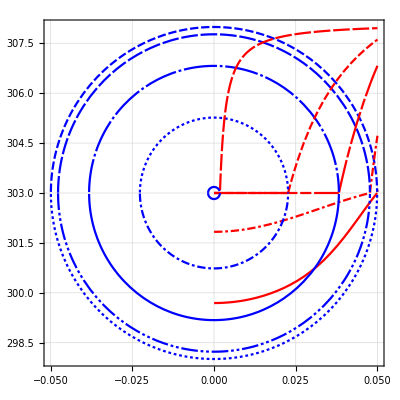

```mathematica
t15=15*60*60;
t05=5*60*60;
t24=24*60*60;
tp8=0.8*60*60;
tp1=0.1*60*60;
Plot[
{
Piecewise[{{Ts[r,tp1],0<r<sFunc[tp1]},{Tl[r,tp1],r>sFunc[tp1]}}],
100sFunc[tp1] √(1-(r/sFunc[tp1])^2)+Tm,-100sFunc[tp1] √(1-(r/sFunc[tp1])^2)+Tm,
Piecewise[{{Ts[r,tp8],0<r<sFunc[tp8]},{Tl[r,tp8],r>sFunc[tp8]}}],
100sFunc[tp8] √(1-(r/sFunc[tp8])^2)+Tm,-100sFunc[tp8] √(1-(r/sFunc[tp8])^2)+Tm,
Piecewise[{{Ts[r,t05],0<r<sFunc[t05]},{Tl[r,t05],r>sFunc[t05]}}],
100sFunc[t05] √(1-(r/sFunc[t05])^2)+Tm,-100sFunc[t05] √(1-(r/sFunc[t05])^2)+Tm,
Piecewise[{{Ts[r,t15],0<r<sFunc[t15]},{Tl[r,t15],r>sFunc[t15]}}],
100sFunc[t15] √(1-(r/sFunc[t15])^2)+Tm,-100sFunc[t15] √(1-(r/sFunc[t15])^2)+Tm,
Piecewise[{{Ts[r,t24],0<r<sFunc[t24]},{Tl[r,t24],r>sFunc[t24]}}],
100sFunc[t24] √(1-(r/sFunc[t24])^2)+Tm,-100sFunc[t24] √(1-(r/sFunc[t24])^2)+Tm
},
{r,-R,R}, PlotTheme->{"Detailed","Monochrome", "CoolColor"},AspectRatio->1,PlotLegends->None,PlotRange->{298,308},PlotStyle->{Red,Blue,Blue}]
```